```mathematica
ClearAll["Global'^*"]
Clear[θ,ϕ,ψ,θd0,ϕd0,ψd0,EOM,ω1,ω2,ω3]
Object =Ellipsoid[{0,0,0},{3,2,1.5}];
centerofmass = RegionCentroid[Object];
I1 = NIntegrate[(y-centerofmass[[2]])^2+(z-centerofmass[[3]])^2,{x,y,z}∈Object];
I2 = NIntegrate[(x-centerofmass[[1]])^2+(z-centerofmass[[3]])^2,{x,y,z}∈ Object];
I3 = NIntegrate[(x-centerofmass[[1]])^2+(y-centerofmass[[2]])^2,{x,y,z}∈ Object];
(*Alternatively, Use MomentOfINertia[Object] to get I1, I2 and I3 immediately*)
```

```mathematica
rplc={ω1[t] == ϕ'[t]Sin[θ[t]]Sin[ψ[t]] + θ'[t] Cos[ψ[t]],
ω2[t] == ϕ'[t]Sin[θ[t]]Cos[ψ[t]]-θ'[t]Sin[ψ[t]],
ω3[t] == ϕ'[t]Cos[θ[t]]+ψ'[t]};
tmax = 100;
θ0 = 0.1;
ϕ0 = 0.1;
ψ0 = 0.1;
ω10 =.01;
ω20 = 1.;
ω30 = 0.01;
```

```mathematica
EOM = {I1 ω1'[t] == ω2[t] ω3[t] (I2-I3), I2 ω2'[t] == ω3[t] ω1[t] (I3 - I1), I3 ω3'[t] == ω1[t] ω2[t] (I1 - I2)};
Initialcondition = {θ[0]==θ0, ϕ[0]==ϕ0,ψ[0]==ψ0,ω1[0]==ω10, ω2[0]==ω20,ω3[0]==ω30};
```

```mathematica
{θ[t_],ϕ[t_],ψ[t_]}={θ[t],ϕ[t],ψ[t]}/. NDSolve[Join[rplc,EOM,Initialcondition],{θ[t],ϕ[t],ψ[t]},{t,0,tmax}][[1]];
{ω1[t_],ω2[t_],ω3[t_]} = { ϕ'[t]Sin[θ[t]]Sin[ψ[t]] + θ'[t] Cos[ψ[t]], ϕ'[t]Sin[θ[t]]Cos[ψ[t]]-θ'[t]Sin[ψ[t]], ϕ'[t]Cos[θ[t]]+ψ'[t]};
```

```mathematica
g = {Object,
{Red,Thick,Arrowheads[0.01],Arrow[{{0,0,0},{0,0,3}}],Text[Style["z",Medium],{0,0,3.5}]},{Blue,Thick,Arrowheads[0.01],Arrow[{{0,0,0},{0,3,0}}],Text[Style["y",Medium],{0,3.5,0}]},{Green,Thick,Arrowheads[0.01],Arrow[{{0,0,0},{3,0,0}}],Text[Style["x",Medium],{3.5,0,0}]}};

Animate[
Grid[{
{Grid[{
{"Time","ω_x","ω_y","ω_z"},{PaddedForm[t,{4,3}],PaddedForm[ω1[t],{4,3}],PaddedForm[ω2[t],{3,4}],PaddedForm[ω3[t],{3,4}]}
},Frame->All]
},

{Grid[{
{"Ix","Iy","Iz"},{PaddedForm[I1,{4,3}],PaddedForm[I2,{4,3}],PaddedForm[I3,{4,3}]}},Frame->All]
},

{Graphics3D[
{GeometricTransformation[GraphicsGroup[g],EulerMatrix[{ϕ[t],θ[t],ψ[t]},{3,1,3}]]},
PlotRange->{{-5,5},{-5,5},{-5,5}},AxesLabel->{"x","y","z"}, Boxed->False,ImageSize->Medium]}}],{t,0,tmax},AnimationRate->8]
```

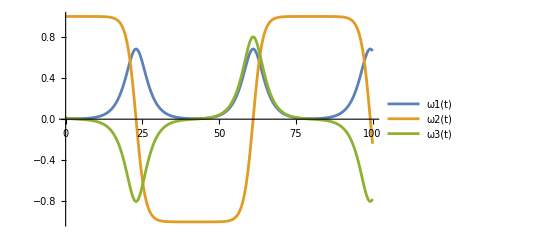

```mathematica
Plot[{ω1[t],ω2[t],ω3[t]},{t,0,tmax},PlotLegends->"Expressions"]
```